```mathematica
eqn = (y')^2/(x*(1+(y')^2))==c;
Solve[eqn,y']
```

{{y'→-(√c √x)/(√(1-c x))},{y'→(√c √x)/(√(1-c x))}}

```mathematica
y[x_]:= ∫_0^x (√(c*u))/(1-c*u)ⅆu
```

```mathematica
y = ∫1/c Tan[θ]Sin[2θ]ⅆθ //Expand
```

θ/c-(sin(2 θ))/(2 c)

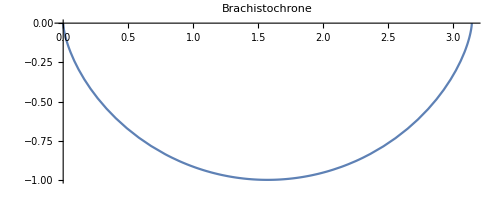

```mathematica
ParametricPlot[{1/2(2θ-Sin[2θ]),-1/2(1-Cos[2θ])},{θ,0,π},PlotLabel->"Brachistochrone",AspectRatio->Automatic]
```